```mathematica
data0={
{1.140225,0.106240},{1.248375,0.050715},{1.356525,0.018540},{1.464675,0.009280},{1.572825,0.006165},{1.680975,0.004585},{1.789125,0.004000},{1.897275,0.004150},{2.005425,0.004470},{2.113575,0.004170},{2.221725,0.004720},{2.329875,0.005020},{2.438025,0.005695},{2.546175,0.005800},{2.654325,0.006275},{2.762475,0.006875},{2.870625,0.007000},{2.978775,0.008195},{3.086925,0.008500},{3.195075,0.009400},{3.303225,0.009420},{3.411375,0.010150},{3.519525,0.010795},{3.627675,0.011310},{3.735825,0.011780},{3.843975,0.012995},{3.952125,0.013320},{4.060275,0.014155},{4.168425,0.014320},{4.276575,0.015480},{4.384725,0.015175},{4.492875,0.016090},{4.601025,0.016810},{4.709175,0.017005},{4.817325,0.017250},{4.925475,0.017770},{5.033625,0.017940},{5.141775,0.018040},{5.249925,0.018580},{5.358075,0.017995},{5.466225,0.018495},{5.574375,0.018920},{5.682525,0.018550},{5.790675,0.018705},{5.898825,0.018130},{6.006975,0.017810},{6.115125,0.017780},{6.223275,0.017460},{6.331425,0.017440},{6.439575,0.016390},{6.547725,0.015650},{6.655875,0.015210},{6.764025,0.014950},{6.872175,0.014445},{6.980325,0.013580},{7.088475,0.013080},{7.196625,0.011960},{7.304775,0.011870},{7.412925,0.011000},{7.521075,0.009800},{7.629225,0.009645},{7.737375,0.008850},{7.845525,0.008020},{7.953675,0.007345},{8.061825,0.006650},{8.169975,0.006300},{8.278125,0.005770},{8.386275,0.004950},{8.494425,0.004410},{8.602575,0.003850},{8.710725,0.003410},{8.818875,0.002965},{8.927025,0.002795},{9.035175,0.002225},{9.143325,0.002100},{9.251475,0.001605},{9.359625,0.001295},{9.467775,0.001240},{9.575925,0.000960},{9.684075,0.000840},{9.792225,0.000590},{9.900375,0.000470},{10.008525,0.000430},{10.116675,0.000295},{10.224825,0.000240},{10.332975,0.000245},{10.441125,0.000155},{10.549275,0.000090},{10.657425,0.000065},{10.765575,0.000080},{10.873725,0.000010},{10.981875,0.000040},{11.090025,0.000040},{11.198175,0.000010},{11.306325,0.000015},{11.414475,0.000000},{11.522625,0.000005},{11.630775,0.000005},{11.738925,0.000005}
};
```

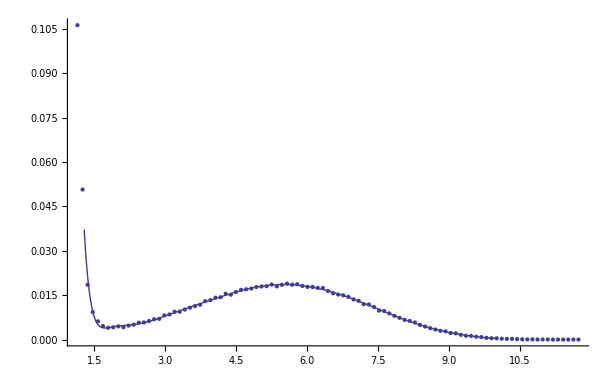

```mathematica
FE=Fit[data0,{1,Log[x],x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14},x];
FEout=Fit[data0,{1,Log[xout],xout,xout^2,xout^3,xout^4,xout^5,xout^6,xout^7,xout^8,xout^9,xout^10,xout^11,xout^12,xout^13,xout^14},xout];
Show[ListPlot[data0],Plot[FE,{x,1.2,10}]]
```

```mathematica
MFPT=NIntegrate[1/FEout NIntegrate[FE,{x,xout,10.5}],{xout,1.2,5.5}]
xc=1.02;
MFPT_unloop=NIntegrate[1/FEout NIntegrate[FE,{x,xc,xout}],{xout,1.2,5.5}]
```

NIntegrate::nlim: x = xout is not a valid limit of integration.

37.1501

NIntegrate::nlim: x = xout is not a valid limit of integration.

21.2425